```mathematica
Clear["Global`*"]
```

```mathematica
fun[x_] := Exp[-2 * x] +1/2  * Exp[-3/2 *x]
```

```mathematica
fun[x]
```

ⅇ^(-2 x)+1/2 ⅇ^(-3 x/2)

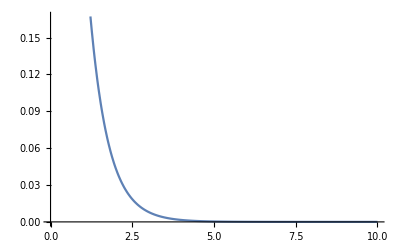

```mathematica
Plot[{fun[k]}, {k,0,10}]
```

```mathematica
invfun[k_] := LaplaceTransform[fun[m],m,k]
```

```mathematica
invfun[x]
```

1/(2 (3/2+x))+1/(2+x)

```mathematica
lambda = 10^{-2};  b = 1 ; theta = 0.1 ; u = 0.5
c = lambda * (1+theta)* Integrate[per*fun[per], {per, 0, Infinity}]
```

0.5

{0.00519444}

```mathematica
phiinv[k_, c_, theta_, lambda_] := c * (theta/(1+theta)) / (c*k - lambda * (1 - invfun[k]))
```

```mathematica
phiinv[s, c, theta, lambda]
```

{0.000472222/(0.00519444 s+1/100 (-1+1/(2 (3/2+s))+1/(2+s)))}

```mathematica
phi[w_]:= InverseLaplaceTransform[phiinv[s, c, theta, lambda], s, w]
```

```mathematica
phi[w]
```

{0.000472222 (-4.30132 ⅇ^(-1.74611 w)-133.233 ⅇ^(-0.661773 w)+330.047 ⅇ^(0.833012 w))}

```mathematica
psi[w_] := 1 - phi[w]
```

```mathematica
psi[w]
```

{1-0.000472222 (-4.30132 ⅇ^(-1.74611 w)-133.233 ⅇ^(-0.661773 w)+330.047 ⅇ^(0.833012 w))}

```mathematica
phi[0.5]
```

{0.190339}

```mathematica
bigx[z_, b_] := (1-psi[z]) / (1-psi[b])
```

```mathematica
bigx[1-z,1]
```

{0.00144991 (759.188 ⅇ^(-0.833012 z)-68.7396 ⅇ^(0.661773 z)-0.750373 ⅇ^(1.74611 z))}

```mathematica
pofb := Integrate[bigx[b-x,b]*fun[x],  {x,0,b-0.00000000000001}]
```

```mathematica
pofb
```

{0.488452}

```mathematica
eud := bigx[u,b] * c/(lambda*(1-pofb))
```

```mathematica
eud
```

{0.59344}